# Tweezer electric field using vector debye theory

## Gabriel Patenotte June 1, 2023

### References

[1] Chen, B . & Pu, J . Tight focusing of elliptically polarized vortex beams . Appl Optics 48, 1288 (2009) .

### Setup

```mathematica
$Assumptions={k>0,r>0,0<=θ<2π,z>0};
um=10^-6;nm=10^-9;MHz=10^6;mm=10^-3;
```

### Incident electric field

```mathematica
(*ℰ[j_]=Switch[j,x,Cos[γ],y,ⅈ Sin[γ]];*)
{χ,ψ}=.;
ℰ[j_]=Switch[j,x,Cos[χ]Cos[ψ]-ⅈ Sin[χ]Sin[ψ],y,ⅈ Cos[ψ]Sin[χ]+Cos[χ]Sin[ψ],z,0];
ℰRe[evec_,t_]:=ComplexExpand[Re[evec Exp[-ⅈ t]]];
Manipulate[ParametricPlot[ℰRe[{ℰ[x],ℰ[y]}/.{χ->χ1,ψ->ψ1},t],{t,0,2π}],{χ1,0,π/4},{ψ1,0,π}];
```

```mathematica
ℰRe[{ℰ[x],ℰ[y]},t]
```

{Cos[t] Cos[χ] Cos[ψ]-Sin[t] Sin[χ] Sin[ψ],Cos[ψ] Sin[t] Sin[χ]+Cos[t] Cos[χ] Sin[ψ]}

### Equations to find near-focus electric fields

Pupil apodization function from reference [1].

```mathematica
A[j_,m_:0]=ℰ[j]((√2 f Sin[θ])/w0)^Abs[m] Exp[-(f^2 Sin[θ]^2)/w0^2]Exp[ⅈ m ϕ];
```

Integrands for computing the electric field near the focus from reference [1]. Assuming a Gaussian beam with m = 0.

```mathematica
exInt[r_,ϕ_,z_]=FullSimplify[-(ⅈ k f)/2 Sin[θ] √Cos[θ] Exp[ⅈ k z Cos[θ]](A[x](1+Cos[θ])ⅈ^m BesselJ[m,k r Sin[θ]]Exp[ⅈ m ϕ]+1/2(A[x]+(-ⅈ)A[y])(Cos[θ]-1)ⅈ^(m+2)BesselJ[m+2,k r Sin[θ]]Exp[ⅈ (m+2)ϕ]+1/2(A[x]+ⅈ A[y])(Cos[θ]-1)ⅈ^(m-2)BesselJ[m-2,k r Sin[θ]]Exp[ⅈ (m-2)ϕ])/.m->0];
eyInt[r_,ϕ_,z_]=FullSimplify[-(ⅈ k f)/2 Sin[θ] √Cos[θ] Exp[ⅈ k z Cos[θ]](A[y](1+Cos[θ])ⅈ^m BesselJ[m,k r Sin[θ]]Exp[ⅈ m ϕ]+1/2(-ⅈ A[x]-A[y])(Cos[θ]-1)ⅈ^(m+2)BesselJ[m+2,k r Sin[θ]]Exp[ⅈ (m+2)ϕ]+1/2(ⅈ A[x]- A[y])(Cos[θ]-1)ⅈ^(m-2)BesselJ[m-2,k r Sin[θ]]Exp[ⅈ (m-2)ϕ])/.m->0];
ezInt[r_,ϕ_,z_]=FullSimplify[-(ⅈ k f)/2 Sin[θ]^2 √Cos[θ] Exp[ⅈ k z Cos[θ]]((A[x]+(-ⅈ)A[y])ⅈ^(m+1)BesselJ[m+1,k r Sin[θ]]Exp[ⅈ(m+1)ϕ]+(A[x]+ⅈ A[y])ⅈ^(m-1)BesselJ[m-1,k r Sin[θ]]Exp[ⅈ (m-1)ϕ])/.m->0];
```

### Electric field near the focus

Constants that describe our experiment. 
	f: objective focal length of 18 mm
	k: wavenumber for a 1064 nm tweezer
	γ: ellipticity of the incident beam
	w0: beam waist (radius) of 9 mm

```mathematica
experiment=Association[f->18 mm,k->(2π)/(1064 nm),χ->1/2 ArcCos[1/3],w0->9 mm,ψ->0,θNA->0.55,mNaCs->Entity["Element","Sodium"][EntityProperty["Element","AtomicMass"]] + Entity["Element","Cesium"][EntityProperty["Element","AtomicMass"]],mCs-> Entity["Element","Cesium"][EntityProperty["Element","AtomicMass"]],α0->(1870+2 460)/3 4π Quantity["Permittivity of free space"] Quantity["Bohr Radius"]^3,h->Quantity["Planck constant"],ℏ->Quantity["Reduced Planck constant"],λ->Quantity[1064,"Nanometers"]];
exIntN[r_,ϕ_,z_]=exInt[r,ϕ,z]/.experiment;
eyIntN[r_,ϕ_,z_]=eyInt[r,ϕ,z]/.experiment;
ezIntN[r_,ϕ_,z_]=ezInt[r,ϕ,z]/.experiment;
evIntN[r_,ϕ_,z_]={exIntN[r,ϕ,z],eyIntN[r,ϕ,z],ezIntN[r,ϕ,z]};
```

Numerically evaluating the integrals to find the electric fields. 0.55 is the NA of our objective. The inverse square root of intFocus normalizes the peak electric field to be one.

```mathematica
ϵ=10^-16;
With[{ev0=NIntegrate[evIntN[0,0,0],{θ,0,ArcSin[experiment[θNA]]},AccuracyGoal->5]},intFocus=ev0*.ev0];
ev[r_,ϕ_,z_]:=1/(√intFocus)NIntegrate[evIntN[r,ϕ,z],{θ,0,ArcSin[experiment[θNA]]},AccuracyGoal->5];
evc[x_,y_,z_]:=ev[√(x^2+y^2),ArcTan[y/(x+ϵ)],z]
ex[r_,ϕ_,z_]:=1/(√intFocus)NIntegrate[exIntN[r,ϕ,z],{θ,0,ArcSin[experiment[θNA]]},AccuracyGoal->5];
ey[r_,ϕ_,z_]:=1/(√intFocus)NIntegrate[eyIntN[r,ϕ,z],{θ,0,ArcSin[experiment[θNA]]},AccuracyGoal->5];
ez[r_,ϕ_,z_]:=1/(√intFocus)NIntegrate[ezIntN[r,ϕ,z],{θ,0,ArcSin[experiment[θNA]]},AccuracyGoal->5];
```

Intensity near the focus

```mathematica
iv[r_,ϕ_,z_]:=With[{e=ev[r,ϕ,z]},e*.e]
ix[r_,ϕ_,z_]:=Abs[ex[r,ϕ,z]]^2
iy[r_,ϕ_,z_]:=Abs[ey[r,ϕ,z]]^2
iz[r_,ϕ_,z_]:=Abs[ez[r,ϕ,z]]^2
```

```mathematica
ivc[x_,y_,z_]:=iv[√(x^2+y^2),ArcTan[y/(x+ϵ)],z];
```

### Gaussian beam intensity

```mathematica
xM=3;yM=3;zM=15;xRes=0.1;yRes=0.1;zRes=0.1;
xRange=Range[-xM,xM,xRes]um;
yRange=Range[-yM,yM,yRes]um;
zRange=Range[-zM,zM,zRes]um;
ixAxis=ParallelTable[{x,ivc[x,0,0]},{x,xRange}];
iyAxis=ParallelTable[{y,ivc[0,y,0]},{y,yRange}];
izAxis=ParallelTable[{z,ivc[0,0,z]},{z,zRange}];
```

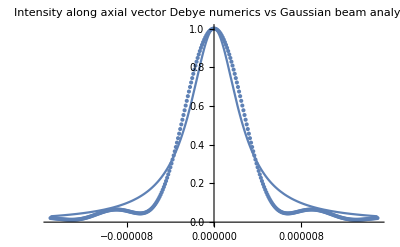

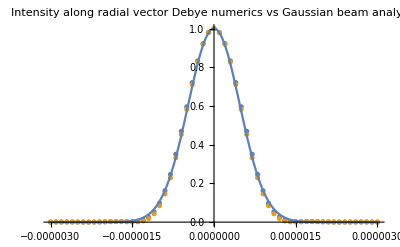

2.64862×10^-6

```mathematica
IGauss[r_,z_,z0_]:=(1/(√(1+(z/z0)^2)))^2 Exp[-(2 r^2)/((1064 nm z0)/π(1+(z/z0)^2))]
nlmZ=NonlinearModelFit[izAxis,IGauss[0,z,z0],{z0},z];
nlmX=NonlinearModelFit[ixAxis,IGauss[x,0,z0],{z0},x];
nlmY=NonlinearModelFit[iyAxis,IGauss[y,0,z0],{z0},y];
z0z=Abs[z0]/.nlmZ["BestFitParameters"];
z0x=Abs[z0]/.nlmX["BestFitParameters"];
z0y=Abs[z0]/.nlmY["BestFitParameters"];
z0m=Mean[{z0z,z0x,z0y}];
Show[ListPlot[izAxis],Plot[IGauss[0,z,z0m],{z,-15 um,15 um}],PlotLabel->"Intensity along axial\nvector Debye numerics vs Gaussian beam analytic",ImagePadding->Automatic]
Show[ListPlot[{ixAxis,iyAxis}],Plot[IGauss[x,0,z0m],{x,-xM um,xM um},PlotRange->All],PlotRange->All,ImagePadding->Automatic,PlotLabel->"Intensity along radial\nvector Debye numerics vs Gaussian beam analytic"
]
z0m
```

```mathematica
z0m (*rayleigh range*)
```

2.64862×10^-6

2.64862×10^-6

### Find trap frequency

```mathematica
ixAxisMin=SortBy[ixAxis,#[[2]]&][[-1,1]];
iyAxisMin=SortBy[iyAxis,#[[2]]&][[-1,1]];
izAxisMin=SortBy[izAxis,#[[2]]&][[-1,1]];
```

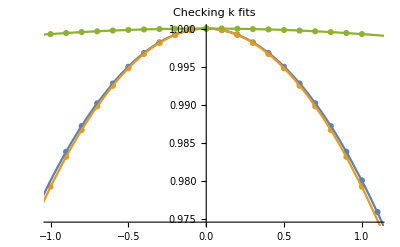

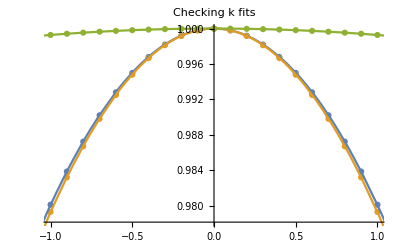

```mathematica
ixAxisNM=ParallelTable[{x,ivc[x,0,0]},{x,ixAxisMin-0.1 um,ixAxisMin+0.1 um,0.01 um}];
iyAxisNM=ParallelTable[{y,ivc[0,y,0]},{y,iyAxisMin-0.1 um,iyAxisMin+0.1 um,0.01 um}];
izAxisNM=ParallelTable[{z,ivc[0,0,z]},{z,izAxisMin-0.1 um,izAxisMin+0.1 um,0.01 um}];
nlmx=NonlinearModelFit[ixAxisNM,1-1/2 k x^2,k,x];
nlmy=NonlinearModelFit[iyAxisNM,1-1/2 k y^2,k,y];
nlmz=NonlinearModelFit[izAxisNM,1-1/2 k z^2,k,z];

kx=k/.nlmx["BestFitParameters"];
ky=k/.nlmy["BestFitParameters"];
kz=k/.nlmz["BestFitParameters"];
Show[ListPlot[{ixAxisNM,iyAxisNM,izAxisNM}],Plot[{nlmx[x],nlmy[x],nlmz[x]},{x,-1 um,1um}],PlotLabel->"Checking k fits"]
```

The intensity is normalized, so I should really call it I/I_0 where I_0=U_0/α_0 is the intensity that gives the trap depth U_0 at the focus. I know that U=Iα_0=-1/2 kx^2, so U/U_0=Iα_0/(I_0 α_0)=I/I_0=-1/2 k/U_0 x^2. This means that the second derivative that I obtain in the fit (the variable called kx, ky, kz) is k/U_0. I also know that the trap frequency is ω=√(k/m) (in angular frequency), so f=ω/(2π)=1/(2π)√(U_0 k/U_0 1/m)

I expect that for a Cs RSC trap depth of 112 MHz, the axial and radial trap frequencies for Cs should be 29 kHz and 150 kHz.

```mathematica
UnitConvert[1/(2π)√(h (112 10^6)/Quantity[1,"Seconds"] kz/(Quantity[1,"Meters"]^2 mCs)/.experiment)]
UnitConvert[1/(2π)√(h (112 10^6)/Quantity[1,"Seconds"] kx/(Quantity[1,"Meters"]^2 mCs)/.experiment)]
```

35091.3 per second

184254. per second

These values are 20% higher. This means that for the trap frequencies we measure, vector Debye says there is less intensity at the focus than we think. This could be because vector debye puts more power at the wings of the tweezers than the standard Gaussian beam formula says there is. The added power on the wings means less power in the center.

```mathematica
{(35-29)/29,(184-150)/150}//N
```

{0.206897,0.226667}

Trap frequency in Hz for a given trap depth U0 in Hz.

```mathematica
fz=√U0 QuantityMagnitude[UnitConvert[1/(2π)√(h 1/Quantity[1,"Seconds"] kz/(Quantity[1,"Meters"]^2 mNaCs)/.experiment)]];
fx=√U0 QuantityMagnitude[UnitConvert[1/(2π)√(h 1/Quantity[1,"Seconds"] kx/(Quantity[1,"Meters"]^2 mNaCs)/.experiment)]];
fy=√U0 QuantityMagnitude[UnitConvert[1/(2π)√(h 1/Quantity[1,"Seconds"] ky/(Quantity[1,"Meters"]^2 mNaCs)/.experiment)]];
```

### Wavefunctions

```mathematica
ψx[x_,n_:0]=1/(√(2^n n!))fx^(1/4)QuantityMagnitude[UnitConvert[((mNaCs 2π Quantity["Hertz"])/(π ℏ))^(1/4)]]Exp[-(mNaCs 2π fx Quantity["Hertz"] x^2 Quantity["Meters"]^2)/(2ℏ)]HermiteH[n,√fx x UnitConvert[√((mNaCs 2π Quantity["Hertz"])/ℏ)Quantity["Meters"]]]/.experiment;
ψy[y_,n_:0]=1/(√(2^n n!))fy^(1/4)QuantityMagnitude[UnitConvert[((mNaCs 2π Quantity["Hertz"])/(π ℏ))^(1/4)]]Exp[-(mNaCs 2π fy Quantity["Hertz"] y^2 Quantity["Meters"]^2)/(2ℏ)]HermiteH[n,√fy y UnitConvert[√((mNaCs 2π Quantity["Hertz"])/ℏ)Quantity["Meters"]]]/.experiment;
ψz[z_,n_:0]=1/(√(2^n n!))fz^(1/4)QuantityMagnitude[UnitConvert[((mNaCs 2π Quantity["Hertz"])/(π ℏ))^(1/4)]]Exp[-(mNaCs 2π fz Quantity["Hertz"] z^2 Quantity["Meters"]^2)/(2ℏ)]HermiteH[n,√fz z UnitConvert[√((mNaCs 2π Quantity["Hertz"])/ℏ)Quantity["Meters"]]]/.experiment;
```

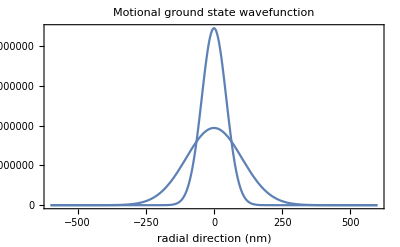

```mathematica
Plot[{Abs[ψz[x nm,0]]^2,Abs[ψx[x nm,0]]^2}/.U0->1MHz,{x,-600 ,600 },PlotRange->All,PlotLabel->"Motional ground state wavefunction",Frame->True,LabelStyle->FontSize->15,FrameLabel->{"radial direction (nm)"}]
```

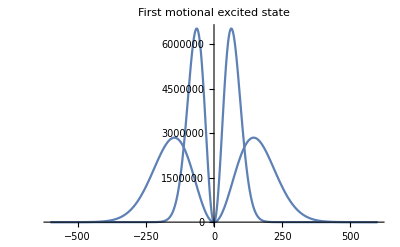

```mathematica
Plot[{Abs[ψz[x nm,1]]^2,Abs[ψx[x nm,1]]^2}/.U0->1MHz,{x,-600 ,600 },PlotRange->All,PlotLabel->"First motional excited state"]
```

```mathematica
fwhm[ψ_,U_]:=Module[{p0,p},p[x_]=Abs[ψ[x nm]]^2/.U0->U;p0=p[0];
Abs[Differences[Quiet[SolveValues[p[x]==p0/2,x]]]][[1]]]
```

```mathematica
{fwhmX,fwhmY,fwhmZ}={fwhm[ψx, 10^6],fwhm[ψy,10^6],fwhm[ψz,10^6]}
```

{105.747,104.685,242.313}

### Ellipticity

```mathematica
findχψ[evec_]:=Module[{χ,ψ,evn,ell,d,tV,pMajor,pMinor},
evn=Normalize[evec];ell=ComplexExpand[Re[(evn)Exp[-ⅈ t]]];d=√(ell[[1]]^2+ell[[2]]^2+ell[[3]]^2);tV=NSolveValues[D[d,t]==0&&0<=t<2π&&d>√(1/2),t][[1]];
pMajor=ell/.t->tV;
pMinor=ell/.t->(tV+π/2);
χ=ArcTan[Norm[pMinor]/Norm[pMajor]];
ψ=ArcTan[pMajor[[2]]/(pMajor[[1]]+ϵ)];
{χ,ψ}
]
```

```mathematica
energy[U0_,χ_]=U0/15(αpar-αperp)/((2αperp+αpar)/3)(-1+3Cos[2χ])/.{αpar->1870,αperp->460}//N;
```

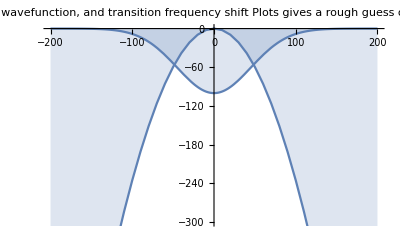

```mathematica
Show[ListPlot[ParallelTable[{x,energy[10^6 ivc[x nm,0,0],findχψ[evc[x nm,0,0]][[1]]]},{x,-200,200, 10}],PlotRange->All,Joined->True,Filling->Axis],Plot[-100 Abs[ψx[x nm,0]]^2/Abs[ψx[0 nm]]^2/.U0->1MHz,{x,-200,200},Filling->Axis],PlotRange->{-300,0},PlotLabel->"Ground motional wavefunction, and transition frequency shift\n Plots gives a rough guess of -50 Hz average shift"]
```

```mathematica
(*With[{e=ℰRe[evc[2 um,0,0],t][[1;;2]]},ParametricPlot[e,{t,0,2π}]]*)
```

```mathematica
eFieldXY=Flatten[With[{r=32,η=2},ParallelTable[{x,y,evc[x nm,y nm,0]},{x,-η fwhmX,η fwhmX,η(2fwhmX)/r},{y,- η fwhmY,η fwhmY,η(2fwhmY)/r}]],1];
coordsXY=eFieldXY[[All,1;;2]];
eXY=eFieldXY[[All,3]];
iXY=ParallelTable[With[{e=eFieldXY[[i,3]]},e*.e],{i,Length[eFieldXY]}];
χψXY=ParallelTable[findχψ[eXY[[i]]],{i,1,Length[eFieldXY]}];
{χXY,ψXY}=χψXYᵀ;
```

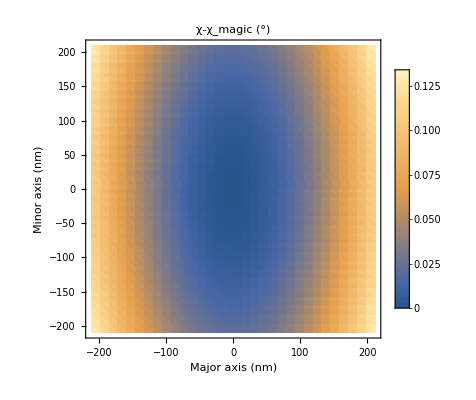

```mathematica
ellipticity=ListDensityPlot[ParallelTable[Flatten[{coordsXY[[i]],180/π χXY[[i]]-180/π 1/2 ArcCos[1/3]}],{i,Length[eFieldXY]}],PlotLegends->Automatic,PlotLabel->"χ-χ_magic (°)",LabelStyle->FontSize->18,Frame->True,FrameLabel->{"Major axis (nm)","Minor axis (nm)"}]
```

```mathematica
SetDirectory["/Volumes/ni_lab/NaCs1pt5/NaCsSimulationPrecomputedMatrices/Images"]
```

/Volumes/ni_lab/NaCs1pt5/NaCsSimulationPrecomputedMatrices/Images

```mathematica
"ellipticityFocalPlane.png"
```

```mathematica
Export["ellipticityFocalPlane.png",ellipticity,ImageResolution->500]
```

ellipticityFocalPlane.png

```mathematica
evc[0 nm,0 nm,0]
```

{0.-0.816497 ⅈ,0.57735+0. ⅈ,0.+0. ⅈ}

Riemann sum of the wavefunction to show that the probability is 1.

```mathematica
ψxyz[x_,y_,z_,nv_:{0,0,0}]:=ψx[x,nv[[1]]]ψy[y,nv[[2]]]ψz[z,nv[[3]]];
```

```mathematica
With[{U1=1 10^6,nvec={0,0,5}},With[{η=2nm,r=10,fwhmX=fwhm[ψx,U1],fwhmY=fwhm[ψy,U1],fwhmZ=fwhm[ψz,U1]},ParallelSum[Abs[ψxyz[x,y,z,nvec]/.U0->U1]^2((2η)/r)^3 fwhmX fwhmY fwhmZ,{x,-η fwhmX,η fwhmX,η(2fwhmX)/r},{y,- η fwhmY,η fwhmY,η(2fwhmY)/r},{z,- η fwhmZ,η fwhmZ,η(2fwhmZ)/r}]]]
```

0.987565

```mathematica
envec[nvec_]:=Module[{eFieldXYZ,coordsXYZ,eXYZ,pXYZ,iXYZ,χψXYZ,χXYZ,ψXYZ},eFieldXYZ=
Flatten[With[{U1=1 10^6},With[{η=2nm,r=10,fwhmX=fwhm[ψx,U1],fwhmY=fwhm[ψy,U1],fwhmZ=fwhm[ψz,U1]},ParallelTable[{x,y,z,evc[x,y,z],Abs[ψxyz[x,y,z,nvec]/.U0->U1]^2((2η)/r)^3 fwhmX fwhmY fwhmZ},{x,-η fwhmX,η fwhmX,η(2fwhmX)/r},{y,- η fwhmY,η fwhmY,η(2fwhmY)/r},{z,- η fwhmZ,η fwhmZ,η(2fwhmZ)/r}]]],2];
coordsXYZ=eFieldXYZ[[All,1;;3]];
eXYZ=eFieldXYZ[[All,4]];
pXYZ=eFieldXYZ[[All,5]];
iXYZ=ParallelTable[With[{e=eFieldXYZ[[i,4]]},e*.e],{i,Length[eFieldXYZ]}];
χψXYZ=ParallelTable[findχψ[eXYZ[[i]]],{i,1,Length[eFieldXYZ]}];
{χXYZ,ψXYZ}=χψXYZᵀ;
Sum[pXYZ[[i]]energy[10^6 iXYZ[[i]],χXYZ[[i]]],{i,Length[eFieldXYZ]}]]
```

```mathematica
tnx=Table[{nx,envec[{nx,0,0}]},{nx,0,5}];
tny=Table[{ny,envec[{0,ny,0}]},{ny,0,5}];
tnz=Table[{nz,envec[{0,0,nz}]},{nz,0,5}];
```

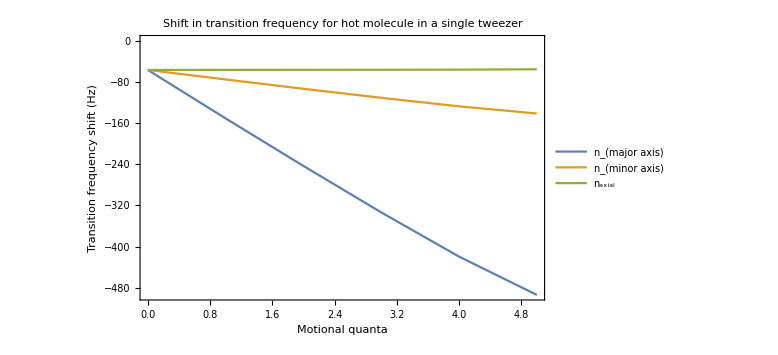

```mathematica
ListPlot[{tnx,tny,tnz},Joined->True,PlotLegends->{"n_(major axis)","n_(minor axis)","n_axial"},Frame->True,FrameLabel->{"Motional quanta","Transition frequency shift (Hz)"},LabelStyle->FontSize->16,PlotLabel->"Shift in transition frequency\n for hot molecule in a single tweezer",ImageSize->Medium]
```

### Two tweezers

```mathematica
θa=π/180 90;
```

```mathematica
eFP[dis_,x_,y_,t_,z_:0]:=evc[x+dis/2 Cos[θa],y+dis/2 Sin[θa],z]+Exp[-ⅈ t]evc[x-dis/2 Cos[θa],y-dis/2 Sin[θa],z];
eFPx[dis_,t_]:=ParallelTable[{x,eFP[dis,x Cos[θa],x Sin[θa],t]},{x,-1.5 dis/2,1.5 dis/2,1.5 dis/12}];
iFPx[dis_,t_]:=With[{eFPxx=eFPx[dis,t]},Table[With[{x=eFPxx[[i,1]],e=eFPxx[[i,2]]},{x,e*.e}],{i,Length[eFPxx]}]];
```

```mathematica
fitD[dis_]:=Module[{θa,i,s},θa=45 π/180;
i=Sum[iFPx[dis,t]/(((2π)/(π/8))+1),{t,0,2π,π/8}];
fit=Fit[i,{1,x^2,x^4,x^6,x^8,x^10,x^12},x]]
```

```mathematica
fits=Table[{d,fitD[d um]},{d,1,3,0.1}];
```

```mathematica
s=Flatten[Table[SolveValues[D[fits[[i,2]],x]==00&&0<x<1.1 fits[[i,1]]/2 um,x],{i,Length[fits]}],1];
peaks=Table[{x/um,fits[[i,2]]}/.x->s[[i-1]],{i,2,Length[fits]}];
```

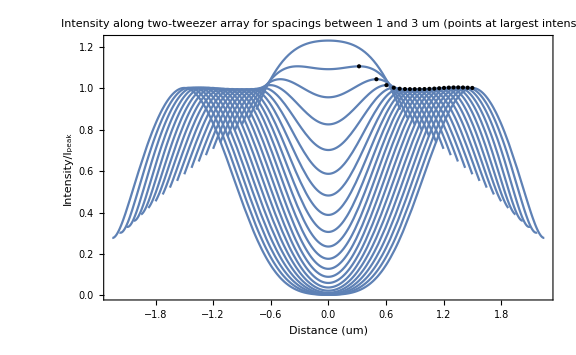

```mathematica
Show[Reverse[Table[Plot[fits[[i,2]]/.x->x1 um,{x1,-1.5 fits[[i,1]]/2,1.5 fits[[i,1]]/2},Epilog->{Point/@peaks}],{i,1,Length[fits]}]],PlotRange->All,Frame->True,FrameLabel->{"Distance (um)","Intensity/I_peak"},LabelStyle->FontSize->18,ImageSize->Large,PlotLabel->"Intensity along two-tweezer array for\nspacings between 1 and 3 um\n(points at largest intensity)"
]
```

```mathematica
beating=Table[{fits[[i,1]],With[{int=With[{e=eFP[fits[[i,1]]um,s[[i-1]]Cos[θa],s[[i-1]] Sin[θa],t]},ComplexExpand[e*.e]]},Abs[(int/.t->π)-(int/.t->0)]]},{i,2,Length[fits]}];
```

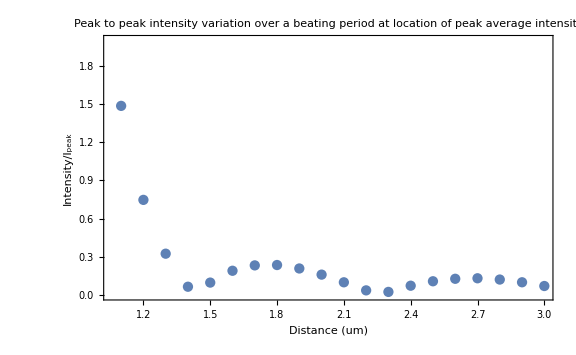

```mathematica
ListPlot[beating,PlotRange->{0,2},Frame->True,FrameLabel->{"Distance (um)","Intensity/I_peak"},LabelStyle->FontSize->18,ImageSize->Large,PlotLabel->"Peak to peak intensity variation over a beating \nperiod at location of peak average intensity"]
```

```mathematica
ωDs=Table[{fits[[i,1]],-1/10^12 Normal[D[Series[fits[[i,2]]/.x->x-s[[i-1]],{x,0,2}],x,x]]},{i,2,Length[fits]}];
```

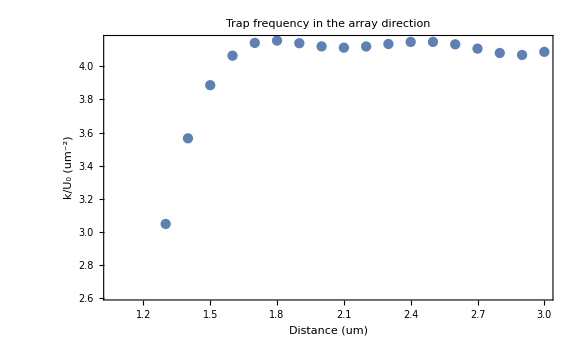

```mathematica
ListPlot[ωDs,Frame->True,FrameLabel->{"Distance (um)","k/U_0 (um^-2)"},LabelStyle->FontSize->18,PlotLabel->"Trap frequency in the array direction",ImageSize->Large]
```

```mathematica
tabY=Table[{fits[[i,1]],Table[{y/um,With[{e=eFP[fits[[i,1]]um,s[[i-1]]Cos[θa]-Sin[θa]y,s[[i-1]] Sin[θa]+Cos[θa]y,t]},1/(2π)NIntegrate[ComplexExpand[e*.e],{t,0,2π}]]},{y,-1um,1um,0.1um}]},{i,2,Length[fits]}];
```

```mathematica
fity=Table[{tabY[[i,1]],Fit[tabY[[i,2]],{1,y^2,y^4,y^6},y]},{i,1,Length[tab]}];
```

```mathematica
ωys={#[[1]],-Normal[D[Series[#[[2]],{y,0,2}],y,y]]}&/@fity;
```

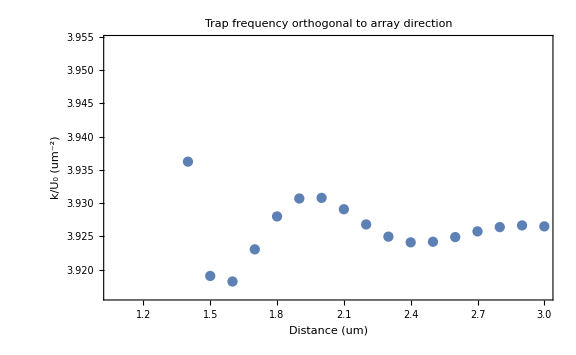

```mathematica
ListPlot[ωys,Frame->True,FrameLabel->{"Distance (um)","k/U_0 (um^-2)"},LabelStyle->FontSize->18,PlotLabel->"Trap frequency orthogonal to array direction",ImageSize->Large]
```

```mathematica
tabZ=Table[{fits[[i,1]],Table[{z/um,With[{e=eFP[fits[[i,1]]um,s[[i-1]]Cos[θa],s[[i-1]] Sin[θa],t,z]},1/(2π)NIntegrate[ComplexExpand[e*.e],{t,0,2π}]]},{z,-1um,1um,0.1um}]},{i,2,Length[fits]}];
```

```mathematica
fitz=Table[{tabZ[[i,1]],Fit[tabZ[[i,2]],{1,z^2,z^4,z^6},z]},{i,1,Length[tab]}];
```

```mathematica
ωzs={#[[1]],-Normal[D[Series[#[[2]],{z,0,2}],z,z]]}&/@fitz;
```

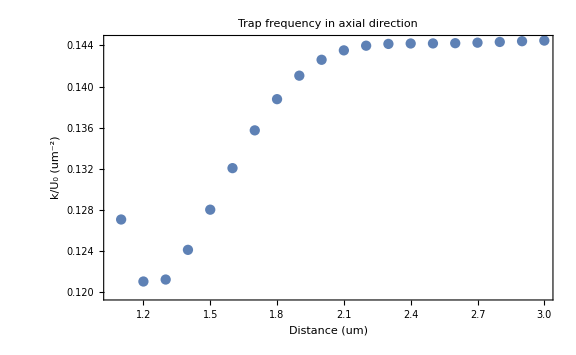

```mathematica
ListPlot[ωzs,Frame->True,FrameLabel->{"Distance (um)","k/U_0 (um^-2)"},LabelStyle->FontSize->18,PlotLabel->"Trap frequency in axial direction",ImageSize->Large]
```

```mathematica
(*eFP[fits[[2,1]]um,s[[2-1]]Cos[θa]-Sin[θa]y+x Cos[θa],s[[2-1]] Sin[θa]+Cos[θa]y+x Sin[θa],t]/.{x->0,y->0}*)
```

```mathematica
NIntegrate[eFP[fits[[2,1]]um,s[[2-1]]Cos[θa],s[[2-1]] Sin[θa],t],{t,0,2π}]
```

```mathematica
Table[{fits[[i,1]],180/π findχψ[1/(2π)NIntegrate[eFP[fits[[i,1]]um,s[[i-1]]Cos[θa],s[[i-1]] Sin[θa],t],{t,0,2π}]][[1]]},{i,2,Length[fits]}]
```

{{1.1,35.6736},{1.2,35.7393},{1.3,34.3794},{1.4,23.7568},{1.5,7.50217},{1.6,23.1621},{1.7,28.1138},{1.8,30.1427},{1.9,31.035},{2.,31.0643},{2.1,29.3126},{2.2,20.4454},{2.3,4.94794},{2.4,21.7972},{2.5,27.3098},{2.6,29.4692},{2.7,30.4815},{2.8,30.9171},{2.9,30.8173},{3.,29.6496}}

```mathematica
intDis=Table[With[{e=eFP[fits[[i,1]]um,s[[i-1]]Cos[θa],s[[i-1]] Sin[θa],t]},{fits[[i,1]],1/(2π)NIntegrate[e*.e,{t,0,2π}]}],{i,2,Length[fits]}];
```

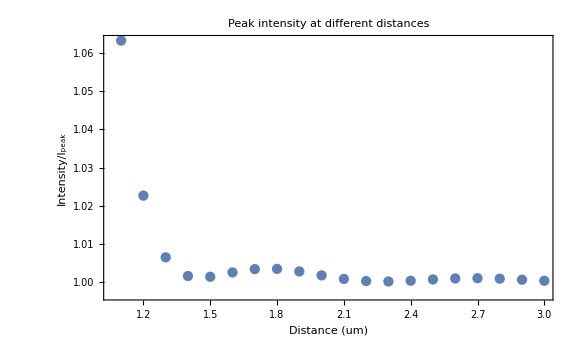

```mathematica
ListPlot[intDis,PlotRange->All,Frame->True,FrameLabel->{"Distance (um)","Intensity/I_peak"},LabelStyle->FontSize->18,ImageSize->Large,PlotLabel->"Peak intensity at different distances"]
```

```mathematica
eEll=Table[With[{e=eFP[fits[[i,1]]um,s[[i-1]]Cos[θa],s[[i-1]] Sin[θa],t]},{fits[[i,1]],e}],{i,2,Length[fits]}];
```

```mathematica
eEllm=Table[With[{e=eFP[fits[[i,1]]um,-s[[i-1]]Cos[θa],-s[[i-1]] Sin[θa],t]},{fits[[i,1]],e}],{i,2,Length[fits]}];
```

```mathematica
tEll=Table[Table[Flatten[{t1,180/π findχψ[eEll[[i,2]]/.t->t1]}],{t1,0,2π,π/32}],{i,1,Length[eEll]}];
```

```mathematica
tEllm=Table[Table[Flatten[{t1,180/π findχψ[eEllm[[i,2]]/.t->t1]}],{t1,0,2π,π/32}],{i,1,Length[eEllm]}];
```

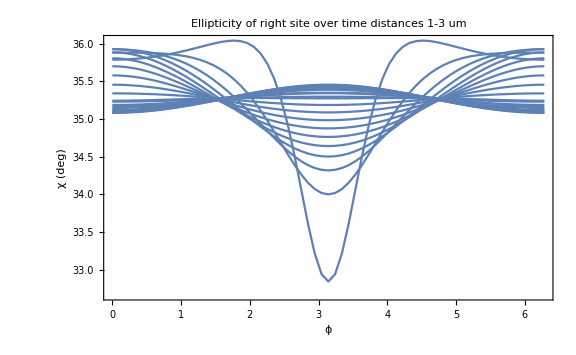

```mathematica
Show[Table[ListPlot[tEll[[i,All,{1,2}]],Joined->True],{i,1,Length[tEll]}],Frame->True,FrameLabel->{"ϕ","χ (deg)"},LabelStyle->FontSize->18,PlotLabel->"Ellipticity of right site over time\ndistances 1-3 um",ImageSize->Large]
```

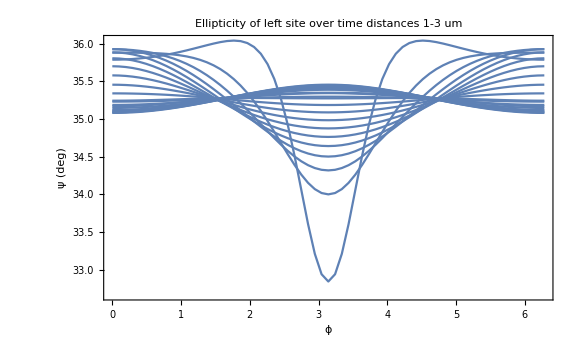

```mathematica
Show[Table[ListPlot[tEllm[[i,All,{1,2}]],Joined->True],{i,1,Length[tEll]}],Frame->True,FrameLabel->{"ϕ","ψ (deg)"},LabelStyle->FontSize->18,PlotLabel->"Ellipticity of left site over time\ndistances 1-3 um",ImageSize->Large]
```

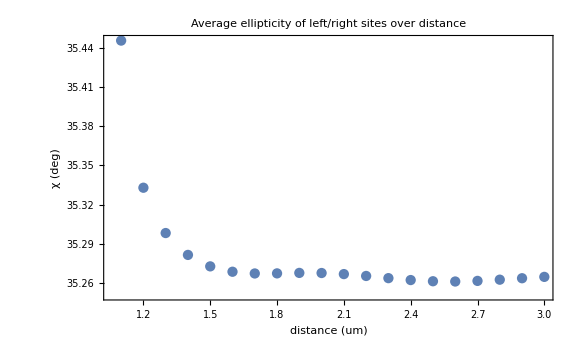

```mathematica
ListPlot[Table[{fits[[i,1]],Mean[tEll[[i-1,All,2]]]},{i,2,Length[fits]}],PlotRange->All,Frame->True,FrameLabel->{"distance (um)","χ (deg)"},LabelStyle->FontSize->18,PlotLabel->"Average ellipticity of left/right sites over distance",ImageSize->Large]
```

```mathematica
tabxy=Flatten[ParallelTable[With[{e=eFP[fits[[2,1]]um,s[[2-1]]Cos[θa]+Cos[θa]x-Sin[θa]y,s[[2-1]] Sin[θa]+Sin[θa]x+Cos[θa]y,π/2]},{x,y,180/π findχψ[e][[1]]}],{x,-200 nm,200 nm,50 nm},{y,-200 nm,200 nm,50 nm}],1];
```

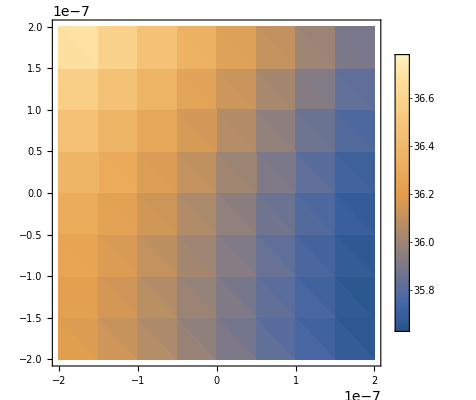

```mathematica
ListDensityPlot[tabxy,PlotLegends->Automatic]
```

```mathematica
180/π findχψ[1/(2π)NIntegrate[eFP[fits[[16,1]]um,s[[16-1]]Cos[θa],s[[16-1]] Sin[θa],t],{t,0,2π}]]
```

{27.3098,-4.5039×10^-10}